```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
ALLQCDtop[mt_, MZ_,  mb_, mc_, p0_, as5MZ_]:= Module[{as5mt, as5mb, as4mb, as4mc, as3mc,as3p0},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as5mb = AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4mc = AlphasExact[as4mb,mb, mc, 4, 4];
as3mc = DecAsDownMS[as4mc, mc, mc, 3, 4];
as3p0 = AlphasExact[as3mc, mc, p0, 3, 4];
Return[(as3p0/as3mc)^(6/27)(as4mc/as4mb)^(6/25)(as5mb/as5mt)^(6/23)((as3p0 + (9π)/16)/(as3mc + (9π)/16))^(-101/576)((as4mc + (50π)/77)/(as4mb + (50π)/77))^(-2047/11550)((as5mb + (23π)/29)/(as5mt + (23π)/29))^(-1375/8004)];]
ALRQCDtop[mt_, MZ_, mb_, mc_, p0_, as5MZ_]:= Module[{as5mt, as5mb, as4mb, as4mc, as3mc,as3p0},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as5mb = AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4mc = AlphasExact[as4mb,mb, mc, 4, 4];
as3mc = DecAsDownMS[as4mc, mc, mc, 3, 4];
as3p0 = AlphasExact[as3mc, mc, p0, 3, 4];
Return[(as3p0/as3mc)^(6/27)(as4mc/as4mb)^(6/25)(as5mb/as5mt)^(6/23)((as3p0 + (9π)/16)/(as3mc + (9π)/16))^(-29/144)((as4mc + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(as5mt + (23π)/29))^(-430/2001)];]
```

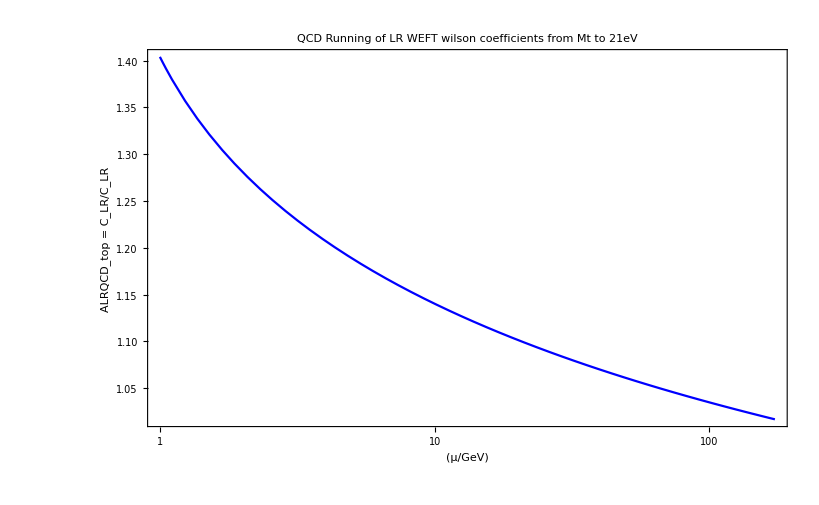

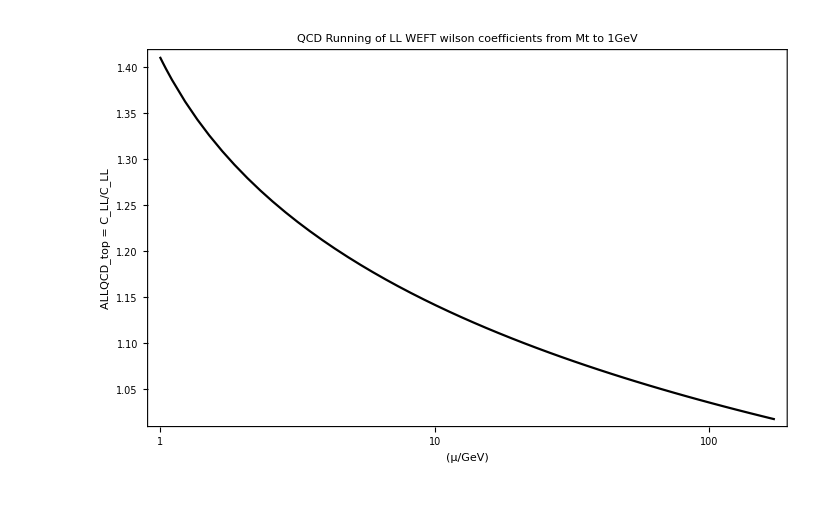

```mathematica
LRtop =LogLinearPlot[ALRQCDtop[173.21, 91.1876, 4.18, 1.28,  p, 0.1185],{p, 1.0, 173.21}, Frame->True,  FrameLabel->{"(μ/GeV)", "ALRQCD_top = C_LR/C_LR"}, PlotLabel->"QCD Running of LR WEFT wilson coefficients from Mt to 21eV", PlotStyle->{Blue}]
LLtop =LogLinearPlot[ALLQCDtop[173.21, 91.1876, 4.18, 1.28, p, 0.1185],{p, 1.0, 173.21}, Frame->True,  FrameLabel->{"(μ/GeV)", "ALLQCD_top = C_LL/C_LL"}, PlotLabel->"QCD Running of LL WEFT wilson coefficients from Mt to 1GeV", PlotStyle->{Black}]
```

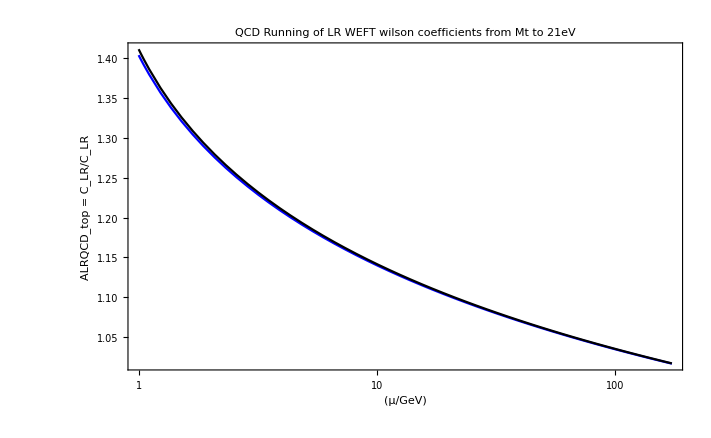

```mathematica
Show[LRtop, LLtop, PlotRange->Automatic]
```